#### Valores experimentales del silicio

```mathematica
hb=6.582119569*10^(-16);
```

```mathematica
datos0=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,1];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Drop[datos1[[All,2]],{1,20}];
(*Se toma a la primera columna como el vector de energía*)
omega=Drop[datos1[[All,1]],{1,20}];
```

```mathematica
parteReKK1=kkrebook[omega,parteIm];
parteReSSKK1=sskkrebook[omega,parteIm,1.65,19.3548];
parteImKK1=kkimbook[omega,parteReKK1];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Transpose[{omega,parteReKK1}]
```

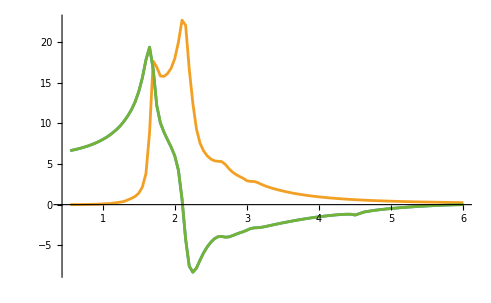

```mathematica
ListLinePlot[{Transpose[{omega,parteReKK1}],Transpose[{omega,parteIm}],Transpose[{omega,parteReSSKK1}]},PlotRange->All]
```

## Modelo de Drude

```mathematica
omegaMin=0.01; (*valor mínimo de energía*)
omegaMax=5; (*valor máximo de energía*)
omega1=Range[omegaMin,omegaMax,0.001]; (*rango de energías*)
omegaPAl=13.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
(*Se define la parte real y la imaginaria del índice de refracción*)
nImagDrude[energy_,omegaP_,gamma_]:=Im[Sqrt[epsDrude[energy,omegaP,gamma]]]
nReDrude[energy_,omegaP_,gamma_]:=Re[Sqrt[epsDrude[energy,omegaP,gamma]]]
```

```mathematica
alRealDrude=Table[{omega,nReDrude[omega,omegaPAl,gammaAl]},{omega,0.01,5,0.001}];
alImagDrude=Table[{omega,nImagDrude[omega,omegaPAl,gammaAl]},{omega,0.01,5,0.001}];
```

```mathematica
omegaconocida=4;
real1=nReDrude[4,omegaPAl,gammaAl];
```

```mathematica
Length[omega1]
Length[alImagDrude[[All,2]]]
```

4991

4991

```mathematica
sale=sskkrebook[omega1, alImagDrude[[All,2]],omegaconocida, real1];
```

```mathematica
parteReKK1Drude=kkrebook[omega1,alImagDrude[[All,2]]];
```

Set::setraw: Cannot assign to raw object {0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»}.

Set::setraw: Cannot assign to raw object 250.175.

Set::setraw: Cannot assign to raw object 239.227.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
ListLinePlot[{Style[Transpose[{omega1,sale}],Dashed],alRealDrude,Transpose[{omega1,parteReKK1Drude}]},PlotRange->All]
```

Transpose::nmtx: The first two levels of {{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},sskkrebook2[{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},{250.175,239.227,229.699,221.31,213.85,«19»,«19»,195.628,190.607,185.994,«4981»},4,0.0633267]} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},sskkrebook2[{0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,«4981»},{250.175,239.227,229.699,221.31,213.85,«19»,«19»,195.628,190.607,185.994,«4981»},4.,0.0633267]} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLinePlot::lpn: {{},{{0.01,233.736},{0.011,221.997},«7»,{0.019,163.504},«4981»},{{0.01,445.403},{0.011,355.613},{0.012,309.967},{0.013,279.609},{0.014,257.089},{0.015,239.343},{0.016,224.806},{0.017,212.568},{0.018,202.051},{0.019,192.867},«4981»}} is not a list of numbers or pairs of numbers.

#### Valores experimentales de eritrocitos

```mathematica
h=4.135667696*10^(-15); (*eV s*)
ℏ=6.582119569*10^(-16); (*eV s*)
c=3*^17 ;(*nm s^-1*)
```

```mathematica
datos0Im=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
datos0Re=Import["C:\\Users\\Poh\\Documents\\Tesis\\Refractive index\\28.7_n_ReN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
datos1Re=Drop[datos0Re,1];
datos2Im=h c/datos1Im[[All,1]];
datos2Re=h c/datos1Re[[All,1]];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Interpolation[Transpose[{datos2Im,datos1Im[[All,2]]}]];
parteRe=Interpolation[Transpose[{datos2Re,datos1Re[[All,2]]}]];
(*Se toma a la primera columna como el vector de energía*)
```

```mathematica
parteImEq=Table[parteIm[x],{x,1.19,4.82,0.01}];
parteReEq=Table[parteRe[x],{x,1.19,4.82,0.01}];
omega=Range[1.19,4.82,0.01];
```

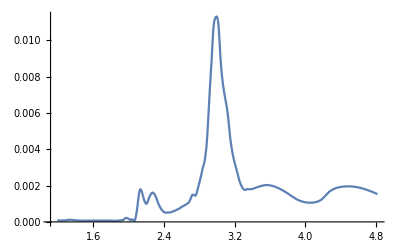

```mathematica
ListLinePlot[Transpose[{omega,parteImEq}],PlotRange->All]
```

```mathematica
parteReKK1=kkrebook[omega,parteImEq];
parteImKK1=kkimbook[omega,parteReKK1];
parteReKK2=kkrebook[omega,parteImKK1];
prueba=selfconsbook[omega,parteReKK1,parteImEq,10,0.6];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

Set::setraw: Cannot assign to raw object 0.0000817065.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object {1.00157,1.00155,1.00154,1.00154,1.00154,1.00154,1.00154,1.00154,1.00155,1.00155,«354»}.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object {-0.00275323,-0.00225203,-0.00201016,-0.00185249,-0.0017363,-0.00164458,-0.00156877,-0.00150387,-0.00144627,-0.00139348,«354»}.

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object {1.00157,1.00155,1.00154,1.00154,1.00154,1.00154,1.00154,1.00154,1.00155,1.00155,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

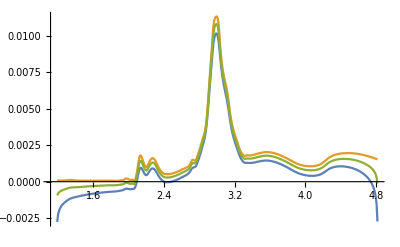

```mathematica
ListLinePlot[{Transpose[{omega,parteImKK1}],Transpose[{omega,parteImEq}],Transpose[{omega,prueba[[2]]}]},PlotRange->All]
```

```mathematica
parteRe[4]
```

1.43294

```mathematica
real1=parteRe[4];
omegaconocida=4;
sale=sskkrebook[omega, parteImEq,omegaconocida, real1];
```

Set::setraw: Cannot assign to raw object {1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,«354»}.

Set::setraw: Cannot assign to raw object 0.0000810247.

Set::setraw: Cannot assign to raw object 0.0000817065.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

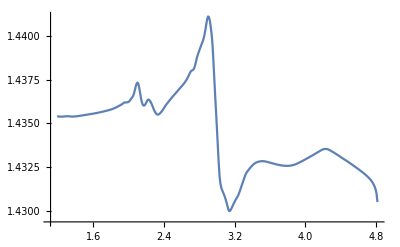

```mathematica
ListLinePlot[Transpose[{omega,sale}]]
```

#### Valores experimentales del oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kau=kau1[[All,2]];
```

```mathematica
ωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
nInterpFunction=Interpolation[Transpose[{ωAu,nau}]];
kInterpFunction=Interpolation[Transpose[{ωAu,kau}]];
```

```mathematica
nAu=Table[nInterpFunction[x],{x,0.65,6.6,0.01}];
kAu=Table[kInterpFunction[x],{x,0.65,6.6,0.01}];
energy=Range[0.65,6.6,0.01];
```

```mathematica
nInterpFunction[3]
```

1.45997

```mathematica
parteReKKAu=kkrebook[energy,kAu];
parteImKKAu=kkimbook[energy,parteReKKAu];
pruebaAu10=selfconsbook[energy,parteReKKAu,kAu,20,0.5];
pruebaSelf=sskkrebook[energy,kAu,3,nInterpFunction[3]];
```

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

2

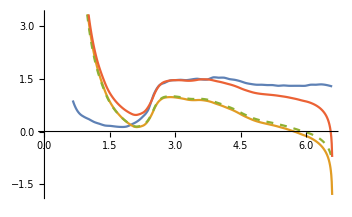

```mathematica
ListLinePlot[{Transpose[{energy,nAu}],Transpose[{energy,parteReKKAu}],Style[Transpose[{energy,pruebaAu10[[1]]}],Dashed],Transpose[{energy,pruebaSelf}]}]
```